### Method ML4EFT

```mathematica
g1[x_, c]:= 1/(1+(1+c x))
```

```mathematica
Animate[Plot[(1/(2+c x)-1)^2, {x, -5, 5}], {c, -5,5 }]
```

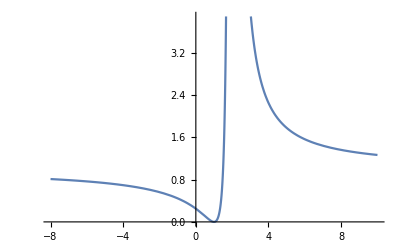

```mathematica
Plot[((1/(2+c x)-1)^2)/.{c-> -1}, {x, -8, 10}]
```

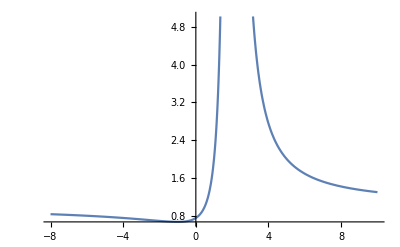

```mathematica
Plot[((1/(2+c x)-1)^2+2*(1/(2+c x))^2)/.{c-> -1}, {x, -8, 10}]
```

### Wulzer’s method

In the following simplified setup, we want to learn the likelihood ratio between the EFT and the SM applied to a total cross section. We restrict ourselves to a single WC such that the  EFT cross section section is given by

```mathematica
σEFT[c_] = 5 + 3c + 1.25 c^2;
```

while

```mathematica
σSM = 5;
```

Consequently, we get for the likelihood ratio

```mathematica
r[c_]= σEFT[c]/σSM//Expand//N
```

1.+0.6 c+0.25 c^2

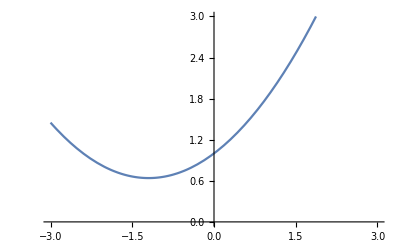

```mathematica
Plot[r[c], {c, -3, 3}, PlotRange->{0, 3}]
```

Wulzer et al parameterise the likelihood ratio by writing

r(c) = (1 + c (NN_11))^2 + c^2 NN_12^2 = 1 + 2c NN_11 + c^2(NN_11^2+ NN_12^2)

Therefore, we have in this case NN_11=0.3 and NN_12=0.4.

Now, can we obtain these same relations from a suitably defined loss? Let us define

```mathematica
gWulzer[NN11_, NN12_,c_]:=1/(1+(1+c NN11)^2+c^2 NN12^2);
LossWulzer[NN11_, NN12_, c_] := σEFT[c]*(gWulzer[NN11, NN12, c])^2+σSM*(gWulzer[NN11, NN12, c]-1)^2
```

One can show that this has a global maximum at NN11 = -1/c and NN12 = 0. Indeed,

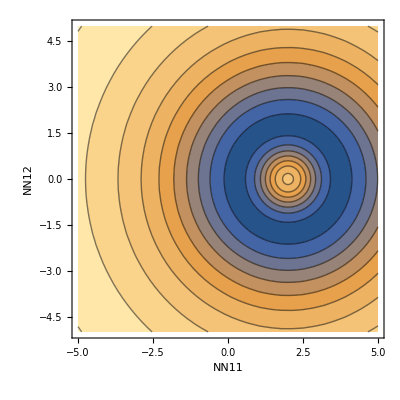

```mathematica
ContourPlot[LossWulzer[NN11, NN12, -1/2] , {NN11, -5, 5}, {NN12, -5, 5}, FrameLabel->{"NN11", "NN12"}]
```

```mathematica
Plot3D[LossWulzer[NN11, NN12, -1/2] , {NN11, -5, 5}, {NN12, -5, 5},AxesLabel->{"NN11", "NN12"}]
```

-Graphics3D-

while the local minima are degenerate as a circle centered about NN11= -1/c, NN12 = 0. From this we can conclude that this loss cannot give us the correct result NN_11=0.3and NN_12=0.4.
However, what happens if we consider multiple c-points, say two?

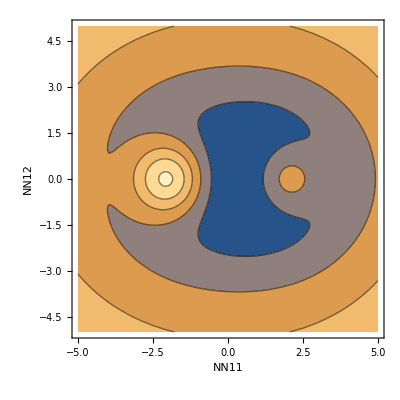

```mathematica
ContourPlot[LossWulzer[NN11, NN12, -1/2] + LossWulzer[NN11, NN12, 1/2] , {NN11, -5, 5}, {NN12, -5, 5}, FrameLabel->{"NN11", "NN12"}]
```

```mathematica
Plot3D[LossWulzer[NN11, NN12, -1/2] + LossWulzer[NN11, NN12, 1/2] , {NN11, -5, 5}, {NN12, -5, 5}, AxesLabel->{"NN11", "NN12"}]
```

-Graphics3D-

This breaks the degeneracy! Let us find the minimum of the loss.

```mathematica
FindMinimum[LossWulzer[NN11, NN12, -2] + LossWulzer[NN11, NN12, 2],{{NN11,0},{NN12,0.2}}]
```

{6.03175,{NN11→0.3,NN12→0.4}}

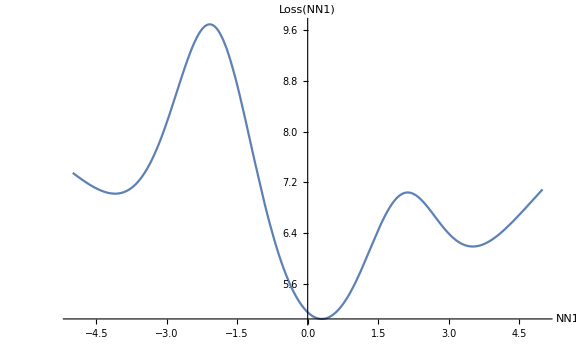

```mathematica
Plot[LossWulzer[nα, 0.4, -1/2] + LossWulzer[nα, 0.4, 1/2] , {nα, -5, 5},ImageSize->Large, AxesLabel->{"NN1", "Loss(NN1)"}]
```

The solutions agree!

### Alternative 1

```mathematica
g[NN1_, NN2_, c1_, c2_]:= 1/(1+(1+c1*NN1 +c2*  NN2 ))
```

```mathematica
Plot3D[g[NN1, NN2, 1, 1]^2, {NN1, 0, 5}, {NN2, 0, 5}, PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[(g[NN1, NN2]-1)^2, {NN1, 0, 5}, {NN2, 0, 5}, PlotRange->All]
```

-Graphics3D-

```mathematica
σsm =1
σeft = 3 * σsm
```

1

3

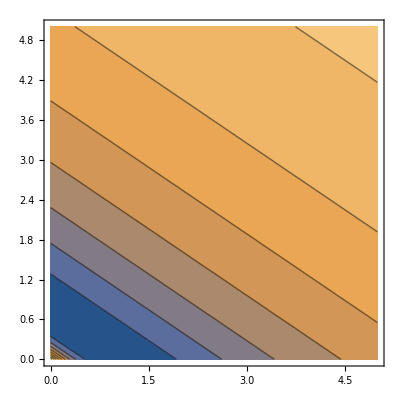

```mathematica
ContourPlot[σsm*(g[NN1, NN2, 2, 3]-1)^2+σeft * g[NN1, NN2, 2, 3]^2, {NN1, 0, 5}, {NN2, 0, 5}, PlotRange->All]
```

```mathematica
L[x_, c_]=2* g1[x, c]^2+(1-g1[x,c])^2
```

2/(2+c x)^2+(1-1/(2+c x))^2

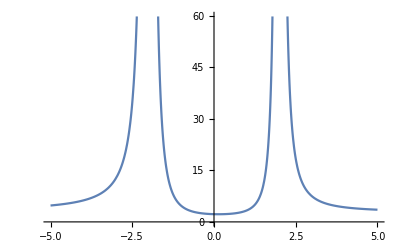

```mathematica
Plot[2*L[x, 1]+L[x, -1], {x, -5, 5}]
```

### Alternative 2

```mathematica
σEFT[c1_, c2_] := 5 - 3c1 + 1.25 c1^2+ 3c2 + 1.25 c2^2+0.5 c1 c2;
```

```mathematica
r[c1_, c2_]:= σEFT[c1, c2]/σEFT[0, 0]
```

```mathematica
r[c1, c2]//Expand
```

1.-0.6 c1+0.25 c1^2+0.6 c2+0.1 c1 c2+0.25 c2^2

```mathematica
Plot3D[σEFT[c1, c2], {c1, -10, 10}, {c2, -10, 10}, PlotRange-> {0, 75}]
```

-Graphics3D-

```mathematica
gAlt2[NN1_, NN2_, NN11_, NN22_,NN12_, c1_, c2_]:=1/(1+Ramp[1+c1 NN1+c2 NN2+c1^2 NN11+ c2^2 NN22+c1 c2 NN12]);
LossAlt2[NN1_, NN2_, NN11_, NN22_,NN12_, c1_, c2_] := σEFT[c1, c2]*(gAlt2[NN1, NN2, NN11, NN22,NN12, c1, c2])^2+σSM*(gAlt2[NN1, NN2, NN11, NN22,NN12, c1, c2]-1)^2
```

```mathematica
Loss = LossAlt2[NN1, NN2, NN11, NN22,NN12, -1, 0] + LossAlt2[NN1, NN2, NN11, NN22,NN12, 1,0]+LossAlt2[NN1, NN2, NN11, NN22,NN12, 0, -1] + LossAlt2[NN1, NN2, NN11, NN22,NN12, 0, 1]+LossAlt2[NN1, NN2, NN11, NN22,NN12, 1, 1] ;
```

```mathematica
sol =FindMinimum[Loss, {{NN1,0},{NN2,0}, {NN11, 0}, {NN22, 0}, {NN12, 0}}]
```

{13.5075,{NN1→-0.6,NN2→0.6,NN11→0.25,NN22→0.25,NN12→0.1}}

```mathematica
Drop[sol[[2]], 1]
```

{NN2→0.6,NN11→0.25,NN22→0.25,NN12→0.1}

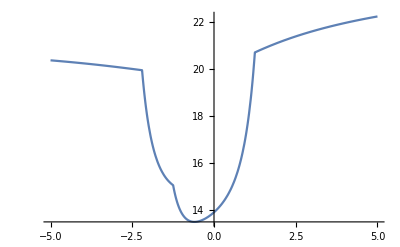

```mathematica
Plot[Loss/.Drop[sol[[2]], 1], {NN1, -5, 5}]
```